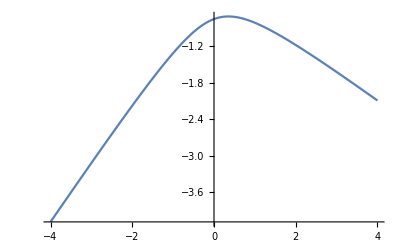

```mathematica
Plot[x-1.5 1/2(x+√(x^2+1)),{x,-4,4}]
```

## unknown disturbance d: we know that |d| <=θ

## <d̂, Proj[μ, d̂]> when |d̂| = θ̂>θ

```mathematica
(*D[x-1/2(x+√(x^2+δ^2))R,x]//Simplify*)
(*Solve[D[x-1/2(x+√(x^2+δ^2))R,x]==0,x]//Simplify*)
Simplify[Maximize[x-1/2(x+√(x^2+δ^2))R,x],R>1&&δ>0]
```

{-√(-1+R) δ,{x→-((-2+R) δ)/(2 √(-1+R))}}

```mathematica
Simplify[Maximize[x-1/2(x+√(x^2+δ^2))R,x],δ>0]
```

{Piecewise[{{-√(-1+R) δ, R>1}, {∞, R<1}, {0, True}}],{x→Piecewise[{{Indeterminate, R≤1}, {-((-2+R) δ)/(2 √(-1+R)), True}}]}}

## When is ((r^2-d^2)/(dd^2-d^2))^(n+1)r^2/d^2>1

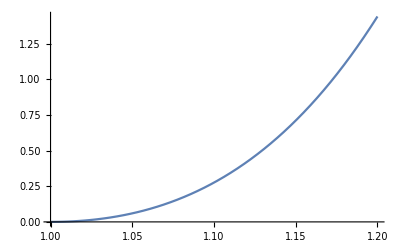

```mathematica
Plot[((r^2-d^2)/(dd^2-d^2))^(n+1)r^2/d^2/.{d-> 1,dd-> 1.2,n-> 1},{r,1,1.2}]
```

## function max(0,((r^2-d^2)/(dd^2-d^2))^(n+1)) is increasing with r for r>d

```mathematica
(*D[((r^2-d^2)/(dd^2-d^2))^2 r^2/d^2,r]-((2 r ((r^2-d^2)/(dd^2-d^2)) (3 r^2/d^2-1))/(dd^2-d^2))//FullSimplify*)
D[((r^2-d^2)/(dd^2-d^2))^(n+1)r^2/d^2,r]-((2 r ((r^2-d^2)/(dd^2-d^2))^n ((2+n) r^2/d^2-1))/(dd^2-d^2))//FullSimplify
```

## function max(0,((r^2-d^2)/(dd^2-d^2))^(n+1)) is is C^n

```mathematica
D[(r^2-d^2)^(n+1),{r,1}]-2 (1+n) r (r^2-d^2)^n//Simplify
D[(r^2-d^2)^(n+1),{r,2}]-2 (1+n) (r^2-d^2)^(n-1) ((1+2 n) r^2-d^2)//Simplify
D[(r^2-d^2)^(n+1),{r,3}]-4 n (1+n) r (r^2-d^2)^(n-2)((1+2 n) r^2-3 d^2) //Simplify
D[(r^2-d^2)^(n+1),{r,4}]-4 n (1+n) (r^2-d^2)^(n-3) (3 d^4+6 d^2 (1-2 n) r^2+(-1+4 n^2) r^4) //Simplify
```

0

0

0

«1 more identical outputs»

## nth derivative of r→max(0,((r^2-d^2)/(dd^2-d^2))^(n+1))

### non-result

```mathematica
nthDeriv[f_,x_,n_]:=n!*SeriesCoefficient[f[x],{x,x,n}]
f[x_]:=1/x
nthDeriv[f,t,n]
```

n! (Piecewise[{{(-t)^-n/t, n≥0}, {0, True}}])

```mathematica
f[x_]:=(x^2-d^2)^n
Simplify[Simplify[nthDeriv[f,x,n],n>0]/.{x->0 }]
```

n! DifferenceRoot[Function[{y,n},{(n-2 n) y[n]-(2+n) d^2 y[2+n]==0,y[0]==(-d^2)^n,y[1]==0}]][n]

```mathematica
InverseFourierTransform[(-I k)^n FourierTransform[(x^2-d^2)^m,x,k],k,x]
```

1/((1+n) (-2 m+n) √π x Gamma[-m])2^(-1+n) √(-1/d^2) (-d^2)^(3/4+m/2+1/4 (-3+2 m-2 n)) (ⅈ^n (-√(-d^2) (2 m-n) (1+n) x Gamma[-m+n/2] Gamma[(1+n)/2] Hypergeometric2F1[(1+n)/2,1/2 (-2 m+n),1/2,x^2/d^2]-2 ⅈ Gamma[1+n/2] Gamma[1/2 (1-2 m+n)] ((d^2-x^2) Hypergeometric2F1[(2+n)/2,1/2 (1-2 m+n),-1/2,x^2/d^2]-(d^2+(-3+2 m-2 n) x^2) Hypergeometric2F1[(2+n)/2,1/2 (1-2 m+n),1/2,x^2/d^2]))+(-ⅈ)^n (-√(-d^2) (2 m-n) (1+n) x Gamma[-m+n/2] Gamma[(1+n)/2] Hypergeometric2F1[(1+n)/2,1/2 (-2 m+n),1/2,x^2/d^2]+2 ⅈ Gamma[1+n/2] Gamma[1/2 (1-2 m+n)] ((d^2-x^2) Hypergeometric2F1[(2+n)/2,1/2 (1-2 m+n),-1/2,x^2/d^2]-(d^2+(-3+2 m-2 n) x^2) Hypergeometric2F1[(2+n)/2,1/2 (1-2 m+n),1/2,x^2/d^2])))

```mathematica
Simplify[1/((1+n) (-2 m+n) √π x Gamma[-m])2^(-1+n) √(-1/d^2) (-d^2)^(3/4+m/2+1/4 (-3+2 m-2 n)) (ⅈ^n (-√(-d^2) (2 m-n) (1+n) x Gamma[-m+n/2] Gamma[(1+n)/2] Hypergeometric2F1[(1+n)/2,1/2 (-2 m+n),1/2,x^2/d^2]-2 ⅈ Gamma[1+n/2] Gamma[1/2 (1-2 m+n)] ((d^2-x^2) Hypergeometric2F1[(2+n)/2,1/2 (1-2 m+n),-1/2,x^2/d^2]-(d^2+(-3+2 m-2 n) x^2) Hypergeometric2F1[(2+n)/2,1/2 (1-2 m+n),1/2,x^2/d^2]))+(-ⅈ)^n (-√(-d^2) (2 m-n) (1+n) x Gamma[-m+n/2] Gamma[(1+n)/2] Hypergeometric2F1[(1+n)/2,1/2 (-2 m+n),1/2,x^2/d^2]+2 ⅈ Gamma[1+n/2] Gamma[1/2 (1-2 m+n)] ((d^2-x^2) Hypergeometric2F1[(2+n)/2,1/2 (1-2 m+n),-1/2,x^2/d^2]-(d^2+(-3+2 m-2 n) x^2) Hypergeometric2F1[(2+n)/2,1/2 (1-2 m+n),1/2,x^2/d^2])))/.{m-> n,x-> d},n∈Integers&&d>0]
```

(2^(-1+n) (ⅈ d)^n (4 ((-ⅈ)^n-ⅈ^n) Gamma[(1-n)/2] Gamma[1+n/2] Hypergeometric2F1[(1-n)/2,(2+n)/2,1/2,1]-((-ⅈ)^n+ⅈ^n) n (1+n) Gamma[-n/2] Gamma[(1+n)/2] Hypergeometric2F1[-n/2,(1+n)/2,1/2,1]))/(n (1+n) √π Gamma[-n])

## Smooth function r→if[x>0,Exp[(x-1)/x],0]: instead of r→max(0,((r^2-d^2)/(dd^2-d^2))^(n+1))

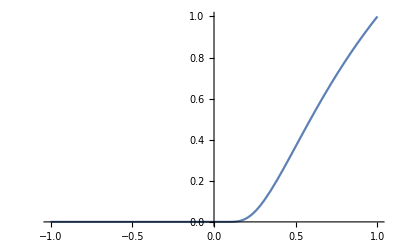

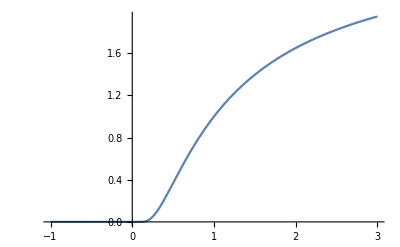

```mathematica
Plot[If[x>0,Exp[(x-1)/x],0],{x,-1,1}]
Plot[If[x>0,Exp[(x-1)/x],0],{x,-1,3}]
```

```mathematica
Limit[D[Exp[(x-1)/x],{x,0}],x-> 0,Direction->-1]
Limit[D[Exp[(x-1)/x],{x,1}],x-> 0,Direction->-1]
Limit[D[Exp[(x-1)/x],{x,2}],x-> 0,Direction->-1]
Limit[D[Exp[(x-1)/x],{x,4}],x-> 0,Direction->-1]
```

0

0

0

«1 more identical outputs»

```mathematica
D[Exp[(x-1)/x],{x,0}]//Simplify
D[Exp[(x-1)/x],{x,1}]//Simplify
D[Exp[(x-1)/x],{x,2}]//Simplify
D[Exp[(x-1)/x],{x,3}]//Simplify
```

ⅇ^((-1+x)/x)

ⅇ^((-1+x)/x)/x^2

(ⅇ^((-1+x)/x) (1-2 x))/x^4

(ⅇ^((-1+x)/x) (1-6 x+6 x^2))/x^6

## derivatives equality: d^p/dx^p e^((x-1)/x)=d^p/dx^p e^(-1/x) because e^((x-1)/x)=e^(1-1/x)=e e^(-1/x) also d^p/dx^p e^(-1/x)=(-1)^p d^p/dy^p e^(1/y) and d^n/dx^n e^(1/x)=(-1)^n e^(1/x)∑_(k=0)^(k=n) (_k^n)(_(k-1)^(n-1))(n-k)!x^(-n-k) and thus d^n/dx^n e^(-1/x)=e^(-1/x)∑_(k=0)^(k=n) (_k^n)(_(k-1)^(n-1))(n-k)!(-x)^(-n-k)

```mathematica
D[Exp[-1/x],{x,0}]//Simplify
D[Exp[-1/x],{x,1}]//Simplify
D[Exp[-1/x],{x,2}]//Simplify
D[Exp[-1/x],{x,3}]//Simplify
```

ⅇ^(-1/x)

ⅇ^(-1/x)/x^2

(ⅇ^(-1/x) (1-2 x))/x^4

(ⅇ^(-1/x) (1-6 x+6 x^2))/x^6